# Infinite 3D medium, Isotropic Point Source, Rayleigh Scattering

## Gamma-4 Random Flight

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
www.eugenedeon.com/hitchhikers

## Path Setup

Put a file at ~/.hitchhikerpath with the path to your hitchhiker repo so that these worksheets can find the MC data from the C++ simulations for verification

```mathematica
SetDirectory[Import["~/.hitchhikerpath"]]
```

## Notation

-Graphics-

c - single-scattering albedo
Σt - extinction coefficient
r - radial position coordinate in medium (distance from point source at origin)
u = cos θ - direction cosine
b - anisotropy parameter

### Namespace

```mathematica
Begin["inf3DisopointRayleighscatterGamma4`"]
```

inf3DisopointRayleighscatterGamma4`

## Analytical results

### Collision rate density

collision rate density Cc due to correlated emission:

#### derivation

```mathematica
pc[s_]:=1/6 Exp[-s] s^3
```

```mathematica
f00=Fpc[0,0,pc];
f01=Fpc[0,1,pc];
f11=Fpc[1,1,pc];
f20=Fpc[2,0,pc];
f22=Fpc[2,2,pc];
```

```mathematica
o=3;
Clear[A,b,c,r,h];
A[n_]:=0;
A[0]:=1;
A[1]:=0;
A[2]:=1/2;
hsystem=Table[h[k]==2/Pi c u F[k,0]+c Sum[A[m]h[m]F[k,m],{m,0,o-1}],{k,0,o-1}];
hsystemsolve=Simplify[Solve[hsystem,Table[h[i],{i,0,o-1}]]/.F[0,0]->f00/.F[0,1]->f01/.F[1,1]->f11/.F[1,0]->-f01/.F[2,0]->f20/.F[0,2]->f20/.F[2,2]->f22]
```

{{h[0]→(2 c u (2 u^5 (-3-2 u^2+u^4)-9 c u (-3-u^2+u^4)+9 c (-3-2 u^2+u^4) ArcTan[u]))/(3 π (u (-2 (u+u^3)^4+3 c^2 (-3-u^2+u^4)+c (9+33 u^2+46 u^4+25 u^6+3 u^8))-3 c (1+u^2) (c (-3+u^2)+3 (1+u^2)^3) ArcTan[u])),h[1]→(8 c u^2 (6 u^5 (1+u^2)^3+27 c (1+u^2)^3 ArcTan[u]+c u (-27-72 u^2-60 u^4-11 u^6+3 u^5 F[1,2]+9 u^7 F[1,2]+9 u^9 F[1,2]+3 u^11 F[1,2])))/(9 π (1+u^2)^2 (2 u^5 (1+u^2)^4+3 c^2 u (3+u^2-u^4)-c u (9+33 u^2+46 u^4+25 u^6+3 u^8)+3 c (1+u^2) (c (-3+u^2)+3 (1+u^2)^3) ArcTan[u])),h[2]→-(16 c u^8 (1+u^2))/(3 π (u (-2 (u+u^3)^4+3 c^2 (-3-u^2+u^4)+c (9+33 u^2+46 u^4+25 u^6+3 u^8))-3 c (1+u^2) (c (-3+u^2)+3 (1+u^2)^3) ArcTan[u]))}}

```mathematica
Clear[r];(2k+1)1/(4 Pi r c)(h[k])j2[k,r u]/.k->0/.hsystemsolve//FullSimplify
```

{(u (-2 u^5 (-3+u^2) (1+u^2)+9 c u (-3-u^2+u^4)-9 c (-3+u^2) (1+u^2) ArcTan[u]) Sin[r u])/(6 π^2 r (2 u^5 (1+u^2)^4+3 c^2 u (3+u^2-u^4)-c u (1+u^2) (9+u^2 (6+u^2) (4+3 u^2))+3 c (1+u^2) (c (-3+u^2)+3 (1+u^2)^3) ArcTan[u]))}

#### result

```mathematica
Ccexact[r_,c_]:=NIntegrate[(u (-2 u^5 (-3+u^2) (1+u^2)+9 c u (-3-u^2+u^4)-9 c (-3+u^2) (1+u^2) ArcTan[u]) Sin[r u])/(6 π^2 r (2 u^5 (1+u^2)^4+3 c^2 u (3+u^2-u^4)-c u (1+u^2) (9+u^2 (6+u^2) (4+3 u^2))+3 c (1+u^2) (c (-3+u^2)+3 (1+u^2)^3) ArcTan[u])),{u,0,Infinity},Method->"LevinRule"]
```

## load MC data

```mathematica
ppoints[xs_,dr_,maxx_]:=Table[{dr(i)-0.5dr,xs[[i]]},{i,1,Length[xs]}][[1;;-2]]
```

```mathematica
ppointsu[xs_,du_,Σt_]:=Table[{-1.0 +du(i)-0.5du,xs[[i]]/(2Σt)},{i,1,Length[xs]}][[1;;-1]]
```

```mathematica
fs=FileNames["code/3D_medium/infinite3Dmedium/Isotropicpointsource/MCdata/inf3D_isotropicpoint_rayleighscatter_gamma4C*"];
```

```mathematica
index[x_]:=Module[{data,c},
data=Import[x,"Table"];
c=data[[2,3]];
{c,data}];
simulations=index/@fs;
cs=Union[#[[1]]&/@simulations]
```

{0.01,0.1,0.3,0.5,0.7,0.8,0.9,0.95,0.99,0.999}

```mathematica
numcollorders=simulations[[1]][[-1]][[2,13]];
```

## Compare analytic and MC

### Collision-rate density - Exact solution (1) comparison to MC

```mathematica
{ActionMenu["Set c","c = "<>ToString[#]:>(c=#;)&/@cs],Dynamic[c]}
```

{Set c,}

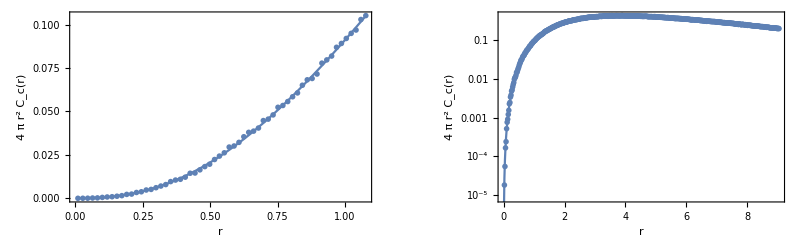

```mathematica
data=SelectFirst[simulations,#[[1]]==c&][[2]];
maxr=data[[2,5]];
dr=data[[2,7]];
MCCollisionRate=ppoints[data[[4]],dr,maxr];
exact1CRShallow=Quiet[{#[[1]],4 Pi (#[[1]])^2 Ccexact[#[[1]],c]}]& /@MCCollisionRate[[1;;60]];
exact1CR=Quiet[{#[[1]],4 Pi (#[[1]])^2 Ccexact[#[[1]],c]}]& /@MCCollisionRate[[61;;-1;;10]];
plotϕshallow=Quiet[Show[
ListPlot[MCCollisionRate[[1;;60]],PlotRange->All,PlotStyle->PointSize[.01]],
ListPlot[exact1CRShallow,PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 π r^2 Subscript[C, "c"][r],},{r,}}
]];
logplotϕ=Quiet[Show[
ListLogPlot[MCCollisionRate,PlotRange->All,PlotStyle->PointSize[.01]],
ListLogPlot[exact1CR,PlotRange->All,Joined->True],
ListLogPlot[exact1CRShallow,PlotRange->All,Joined->True],
Frame->True,
FrameLabel->{{4 π r^2 Subscript[C, "c"][r],},{r,}}
]];
Show[GraphicsGrid[{{plotϕshallow,logplotϕ}},ImageSize->800],PlotLabel->"Infinite 3D, isotropic point source, Rayleigh scattering, Gamma-4 random flight - correlated emission\nCollision-rate density C_c[r], c = "<>ToString[c]]
```

## Namespace

```mathematica
End[]
```

inf3DisopointRayleighscatterGamma4`